## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="u-d";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/

```mathematica
exportdatapath[quarkchannel_]:=basedatapath<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb1=BIDATEXReader[exportdatapath[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
```

< -MemDB- {aBDBIndex,correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

```mathematica
MemDBGet[platdb1,MemDBSelect[platdb1,{numberFilter->Re}],sinkMom]//Union
```

{{-1,0,0}}

```mathematica
v1[v3_]:=v3*0.303;
vinterpolation[gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
vlinks = Union[MemDBGet[platdb1,MemDBSelect[platdb1,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
(*Print[vlinksv3];*)
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
(*Print[vvectoranddata//OutputForm];
Print[groupSamev//OutputForm];*)
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 7]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 8]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 9]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 10]//OutputForm]
```

-6
⟨-360(740) × 10  ⟩_(2902J)

-6
⟨-830(730) × 10  ⟩_(2902J)

-6
⟨-930(650) × 10  ⟩_(2902J)

⟨-0.00137(60)⟩_(2902J)

```mathematica
(*xdata = {6,7,8,9};
ydata =Table[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = etav], {etav, xdata}]
fit = ResamplingFit2D[xdata,ydata,A*Exp[-B*v],v,{A, B}]
Print[fit[[1]]//OutputForm]
fitpara = fitSamples/.fit
fitA= fitpara[[All,2]][[All,1]]
fitB= fitpara[[All,2]][[All,2]]*)
```

```mathematica
AllLinkPathList = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,numberFilter->Re}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
(*Do[Print[i,") ",PathToShift[DistinctLinkPaths[[i+1]],3],"<------->",DistinctLinkPaths[[i+1]], "<------->", MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates],{i,CountDistinct[AllLinkPathList]-1}]*)
Print["linkPaths -> {} are skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]]}],{i,CountDistinct[AllLinkPathList]-1}]
(*bveclinkPathsideNumLIST//MatrixForm*)
bveclinkPathsideNumLISTforbL0=Select[bveclinkPathsideNumLIST,#[[1,1]]==0&];
bveclinkPathsideNumLISTforbLpositive=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&];
bveclinkPathsideNumLISTforbLnegative=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&];
b2list= Union[bveclinkPathsideNumLIST[[All,1]][[All,2]]];
b1list= Union[bveclinkPathsideNumLIST[[All,1]][[All,1]]];
Print["b2 = ",b2list]
Print["b1 = ",b1list]
bveclinkPathsideNumLISTforbL0//MatrixForm
bveclinkPathsideNumLISTforbLpositive//MatrixForm
bveclinkPathsideNumLISTforbLnegative//MatrixForm
bveclinkPathsideNumLISTforbL0//Length
bveclinkPathsideNumLISTforbLpositive//Length
bveclinkPathsideNumLISTforbLnegative//Length
noError=True;
Do[If[(bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bveclinkPathsideNumLISTforbLpositive[",i, "]"];noError=False;],{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found "]];
```

Total No. linkPath = 7225

Total No. Distinct linkPath = 87

linkPaths -> {} are skipped

b2 = {-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

b1 = {-8,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,8}

({0,1,0} | {2}
{0,2,0} | {2,2}
{0,3,0} | {2,2,2}
{0,4,0} | {2,2,2,2}
{0,5,0} | {2,2,2,2,2}
{0,6,0} | {2,2,2,2,2,2}
{0,7,0} | {2,2,2,2,2,2,2}
{0,-1,0} | {-2}
{0,-2,0} | {-2,-2}
{0,-3,0} | {-2,-2,-2}
{0,-4,0} | {-2,-2,-2,-2}
{0,-5,0} | {-2,-2,-2,-2,-2}
{0,-6,0} | {-2,-2,-2,-2,-2,-2}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2})

({1,1,0} | {2,1}
{2,2,0} | {2,1,2,1}
{3,3,0} | {2,1,2,1,2,1}
{4,4,0} | {2,1,2,1,2,1,2,1}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1}
{1,1,0} | {1,2}
{2,2,0} | {1,2,1,2}
{3,3,0} | {1,2,1,2,1,2}
{4,4,0} | {1,2,1,2,1,2,1,2}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2}
{1,2,0} | {2,1,2}
{2,4,0} | {2,1,2,2,1,2}
{3,6,0} | {2,1,2,2,1,2,2,1,2}
{2,1,0} | {1,2,1}
{4,2,0} | {1,2,1,1,2,1}
{6,3,0} | {1,2,1,1,2,1,1,2,1}
{4,1,0} | {1,1,2,1,1}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1}
{1,-1,0} | {-2,1}
{2,-2,0} | {-2,1,-2,1}
{3,-3,0} | {-2,1,-2,1,-2,1}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1}
{1,-1,0} | {1,-2}
{2,-2,0} | {1,-2,1,-2}
{3,-3,0} | {1,-2,1,-2,1,-2}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2}
{1,-2,0} | {-2,1,-2}
{2,-4,0} | {-2,1,-2,-2,1,-2}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2}
{2,-1,0} | {1,-2,1}
{4,-2,0} | {1,-2,1,1,-2,1}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1}
{4,-1,0} | {1,1,-2,1,1}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1})

({-1,1,0} | {2,-1}
{-2,2,0} | {2,-1,2,-1}
{-3,3,0} | {2,-1,2,-1,2,-1}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1}
{-1,1,0} | {-1,2}
{-2,2,0} | {-1,2,-1,2}
{-3,3,0} | {-1,2,-1,2,-1,2}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2}
{-1,2,0} | {2,-1,2}
{-2,4,0} | {2,-1,2,2,-1,2}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2}
{-2,1,0} | {-1,2,-1}
{-4,2,0} | {-1,2,-1,-1,2,-1}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1}
{-4,1,0} | {-1,-1,2,-1,-1}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1}
{-1,-1,0} | {-2,-1}
{-2,-2,0} | {-2,-1,-2,-1}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1}
{-1,-1,0} | {-1,-2}
{-2,-2,0} | {-1,-2,-1,-2}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}
{-1,-2,0} | {-2,-1,-2}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2}
{-2,-1,0} | {-1,-2,-1}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1}
{-4,-1,0} | {-1,-1,-2,-1,-1}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1})

14

36

36

✓ Checked: linkPaths corresponding to   are found

```mathematica
GiveTablePlateauEvenA2BForb[etavalue_]:=(
TablePlateauEvenA2BForb = {};
(*Print["considering only positive b2"];*)
Do[
(*If[ bveclinkPathsideNumLISTforbL0[[i,1]][[2]]<0,Continue[]];*)
bl0g8Re = vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g1Im = vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];


bl0A2B = ((1/(2*Sqrt[2]))*(-bl0g1Im+bl0g8Re));

AppendTo[TablePlateauEvenA2BForb,{bveclinkPathsideNumLISTforbL0[[i,1]],bl0A2B}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];

Do[
(*If[ bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]]<0,Continue[]];*)

blPg8Re = vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg1Im = vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];



blNg8Re=vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg1Im=vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];


blPA2B =(1/(Sqrt[2]*2))*(-blPg1Im+blPg8Re);
blNA2B = (1/(Sqrt[2]*2))*(-blNg1Im+blNg8Re);
blEvenA2B = (blPA2B+blNA2B)/2;

AppendTo[TablePlateauEvenA2BForb,{bveclinkPathsideNumLISTforbLpositive[[i,1]],blEvenA2B}];
AppendTo[TablePlateauEvenA2BForb,{bveclinkPathsideNumLISTforbLnegative[[i,1]],blEvenA2B}];
  ,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
Return[TablePlateauEvenA2BForb];
)
```

```mathematica
PlotA2B[etavalue_]:=(
TablePlateauEvenA2BForb = GiveTablePlateauEvenA2BForb[etavalue];
groupSameb=GroupBy[TablePlateauEvenA2BForb,First->Last];
averagedTablePlateauEvenA2BForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print["\n etavalue = ", etavalue];
(*Print["✓ Same  with different linkPath are averaged\n"];*)
bTlist= Union[averagedTablePlateauEvenA2BForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvenA2BForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL2=Transpose[{Select[averagedTablePlateauEvenA2BForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvenA2BForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL2];
 ,{bT,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Return[Print[PlotbL]];
)
```

etavalue = 8

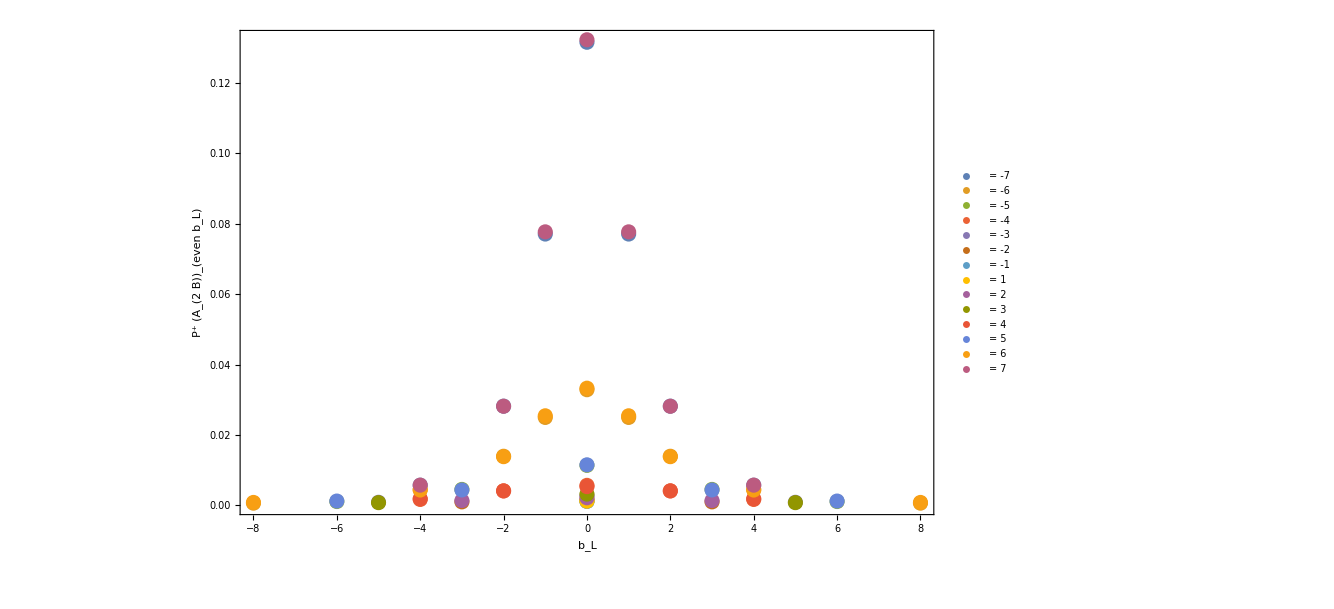

```mathematica
PlotA2B[8]
```

```mathematica
etabvalueerrA2B[etavalue_]:=(
etaaveragedTablePlateauEvenA2BForb={};
TablePlateauEvenA2BForb = GiveTablePlateauEvenA2BForb[etavalue];
groupSameb=GroupBy[TablePlateauEvenA2BForb,First->Last];
averagedTablePlateauEvenA2BForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
bvalueerrbar = MakeErrBars[averagedTablePlateauEvenA2BForb];
Do[
AppendTo[etaaveragedTablePlateauEvenA2BForb, {etavalue, bvalueerrbar[[i]][[1]][[1]][[1]] ,bvalueerrbar[[i]][[1]][[1]][[2]],  bvalueerrbar[[i]][[1]][[2]],  bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[bvalueerrbar]}];
Return[etaaveragedTablePlateauEvenA2BForb]
)
etabvalueerrA2B[8]
```

{{8,0,1,0.131576,0.00125809},{8,0,2,0.0328444,0.000627052},{8,0,3,0.011347,0.000491015},{8,0,4,0.00566994,0.000436171},{8,0,5,0.00276777,0.000409995},{8,0,6,0.0015947,0.000386671},{8,0,7,0.00112656,0.000338516},{8,0,-1,0.13229,0.00120983},{8,0,-2,0.0332764,0.000607873},{8,0,-3,0.0114942,0.000485209},{8,0,-4,0.00529652,0.000434415},{8,0,-5,0.00317313,0.000407779},{8,0,-6,0.00213778,0.000381908},{8,0,-7,0.00123821,0.000365343},{8,1,1,0.077081,0.000802449},{8,-1,1,0.077081,0.000802449},{8,2,2,0.0139349,0.000372378},{8,-2,2,0.0139349,0.000372378},{8,3,3,0.00451384,0.00029844},{8,-3,3,0.00451384,0.00029844},{8,4,4,0.00165778,0.000250911},{8,-4,4,0.00165778,0.000250911},{8,5,5,0.000848382,0.000223957},{8,-5,5,0.000848382,0.000223957},{8,1,2,0.0249639,0.000492652},{8,-1,2,0.0249639,0.000492652},{8,2,4,0.00411137,0.000299597},{8,-2,4,0.00411137,0.000299597},{8,3,6,0.00097371,0.000254695},{8,-3,6,0.00097371,0.000254695},{8,2,1,0.0281652,0.000439043},{8,-2,1,0.0281652,0.000439043},{8,4,2,0.00448023,0.000302701},{8,-4,2,0.00448023,0.000302701},{8,6,3,0.00106776,0.000236027},{8,-6,3,0.00106776,0.000236027},{8,4,1,0.00570806,0.000317156},{8,-4,1,0.00570806,0.000317156},{8,8,2,0.000606565,0.000225011},{8,-8,2,0.000606565,0.000225011},{8,1,-1,0.077706,0.000762565},{8,-1,-1,0.077706,0.000762565},{8,2,-2,0.0138218,0.000369797},{8,-2,-2,0.0138218,0.000369797},{8,3,-3,0.00435302,0.000306096},{8,-3,-3,0.00435302,0.000306096},{8,4,-4,0.00186509,0.000261707},{8,-4,-4,0.00186509,0.000261707},{8,5,-5,0.000758029,0.000220926},{8,-5,-5,0.000758029,0.000220926},{8,1,-2,0.0254326,0.000483536},{8,-1,-2,0.0254326,0.000483536},{8,2,-4,0.00408195,0.000298965},{8,-2,-4,0.00408195,0.000298965},{8,3,-6,0.00134623,0.000238093},{8,-3,-6,0.00134623,0.000238093},{8,2,-1,0.0281482,0.000423749},{8,-2,-1,0.0281482,0.000423749},{8,4,-2,0.00433263,0.000303379},{8,-4,-2,0.00433263,0.000303379},{8,6,-3,0.00120358,0.000251281},{8,-6,-3,0.00120358,0.000251281},{8,4,-1,0.00572222,0.000308829},{8,-4,-1,0.00572222,0.000308829},{8,8,-2,0.000814515,0.000217642},{8,-8,-2,0.000814515,0.000217642}}

```mathematica
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_A2B_err.h5",Table["eta_"<>ToString[n]<>"_bL_bT_A2B_err"->etabvalueerrA2B[n],{n,1,10}]]
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_A2B_err.h5

```mathematica
Import["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_A2B_err.h5","StructureGraph"]
```

-Graphics-

```mathematica
(*baveragedTableA12B[etavalue_]:=(
TablePlateauEvengPlusImForb = GiveTablePlateauEvengPlusImForb[etavalue];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTableA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Return[averagedTableA12B];
)*)
```

```mathematica
(*etafitAofA12B = {};
etafitBofA12B = {};
Do[
foreachb = {};
Do[
AppendTo[foreachb, etabA12B[[i]][[b]][[2]]];
,{i,Length[etabA12B]}];
fit1 = ResamplingFit2D[etalist,foreachb,A*Exp[-B*v],v,{A, B}];
fitpara1 = fitSamples/.fit1;
fitA1= fitpara1[[All,2]][[All,1]];
fitB1= fitpara1[[All,2]][[All,2]];
AppendTo[etafitAofA12B,{etabA12B[[1]][[b]][[1]],fitA1}];
AppendTo[etafitBofA12B,{etabA12B[[1]][[b]][[1]],fitB1}];
,{b,Length[etabA12B[[1]]]}];
etafitAofA12B
etafitBofA12B*)
```

```mathematica
(*newetafitBofA12B= Select[etafitBofA12B,#[[1]]!={4,1,0}&&#[[1]]!={-4,1,0}&&#[[1]]!={3,6,0}&&#[[1]]!={-3,6,0}&&#[[1]]!={6,3,0}&&#[[1]]!={-6,3,0}&&#[[1]]!={8,2,0}&&#[[1]]!={-8,2,0}&&#[[1]]!={3,2,0}&&#[[1]]!={-3,2,0}&];

bTlist= Union[newetafitAofA12B[[All,1]][[All,2]]];
bLlist= Union[newetafitAofA12B[[All,1]][[All,1]]];
PlotbLforDiffbTListforA={};
Do[
PlotbLforAi=Transpose[{Select[newetafitAofA12B, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[newetafitAofA12B, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTListforA,PlotbLforAi];
 ,{bT,bTlist}];
PlotbLforA= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTListforA[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print["A"];
Print[PlotbLforA];
PlotbLforDiffbTListforB={};
Do[
PlotbLforBi=Transpose[{Select[newetafitBofA12B, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[newetafitBofA12B, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTListforB,PlotbLforBi];
 ,{bT,bTlist}];
PlotbLforB= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTListforB[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print["B"];
Print[PlotbLforB];*)
```

```mathematica
(*datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16,25};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist]
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];*)
```